## FTCS Explicit Method Coding

FTCS: Forward Time Centered Space

## Student Name: Roaa Tareq Mohammed Sec. 1 BN. 24

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

## Given Data

```mathematica
tmax = 1.08;
ymax = 0.04;
Δt = 0.002;
Δy = 0.001;
ΔtReq = 0.18;
u0 = 40;
ν = 0.000217;
```

## Initialization

```mathematica
t = Range[0,tmax,Δt];
y = Range[0,ymax,Δy];
tReq = Range[0,tmax,ΔtReq];

raw =Length[y];
col =Length[t];

u = Array[0&,{raw,col}];

d = ν*Δt/Δy^2; DiffusionNumber::boole = "The Scheme is Stable"; 
Which[d<=1/2,Message[DiffusionNumber::boole]];

tReqIndex = Range[1,col,90];
uReq = Array[0&,Length[tReqIndex]];
```

DiffusionNumber::boole: The Scheme is Stable

## Velocity Computation

```mathematica
For[n=1,n<=col,n++,u[[1,n]]=u0]
For[n=1,n<=col-1,n++,
For[j=2,j<=raw-1,j++,u[[j,n+1]]=u[[j,n]]+d*(u[[j+1,n]]-2*u[[j,n]]+u[[j-1,n]])]]
uReq = u[[All, tReqIndex[[#]]]] &/@ Range[1,Length[tReqIndex]];
```

## Table of u(t,y)

```mathematica
tLabel = "t = " <> ToString[#]<> " s"&/@tReq;
yLabel = "y = " <> ToString[#]<> " m"&/@y;

TableForm[uReq[[#]]&/@Range[1,Length[tReqIndex]],
TableDirections->Row,TableHeadings->{tLabel ,yLabel},TableSpacing->{1, 0.5}]
```

| t = 0. s | t = 0.18 s | t = 0.36 s | t = 0.54 s | t = 0.72 s | t = 0.9 s | t = 1.08 s
y = 0. m | 40 | 40 | 40 | 40 | 40 | 40 | 40
y = 0.001 m | 0 | 36.4097 | 37.454 | 37.9192 | 38.197 | 38.3861 | 38.5241
y = 0.002 m | 0 | 32.8645 | 34.9242 | 35.8473 | 36.3998 | 36.7763 | 37.0512
y = 0.003 m | 0 | 29.4077 | 32.4263 | 33.7928 | 34.6139 | 35.1747 | 35.5844
y = 0.004 m | 0 | 26.0795 | 29.9756 | 31.7644 | 32.845 | 33.5851 | 34.1267
y = 0.005 m | 0 | 22.9154 | 27.5865 | 29.7702 | 31.0986 | 32.0115 | 32.6809
y = 0.006 m | 0 | 19.9451 | 25.2721 | 27.8178 | 29.3797 | 30.4577 | 31.2499
y = 0.007 m | 0 | 17.1919 | 23.0444 | 25.9146 | 27.6933 | 28.9272 | 29.8365
y = 0.008 m | 0 | 14.6722 | 20.9137 | 24.0672 | 26.0441 | 27.4235 | 28.4432
y = 0.009 m | 0 | 12.3952 | 18.8887 | 22.2815 | 24.4363 | 25.9498 | 27.0725
y = 0.01 m | 0 | 10.3638 | 16.9764 | 20.5628 | 22.8739 | 24.5091 | 25.7267
y = 0.011 m | 0 | 8.57431 | 15.1821 | 18.9156 | 21.3603 | 23.1041 | 24.4079
y = 0.012 m | 0 | 7.0181 | 13.5091 | 17.3436 | 19.8988 | 21.7373 | 23.1182
y = 0.013 m | 0 | 5.68202 | 11.9592 | 15.8497 | 18.4919 | 20.4109 | 21.8592
y = 0.014 m | 0 | 4.5496 | 10.5324 | 14.4361 | 17.1418 | 19.1268 | 20.6326
y = 0.015 m | 0 | 3.60215 | 9.22738 | 13.1042 | 15.8502 | 17.8866 | 19.4397
y = 0.016 m | 0 | 2.81967 | 8.04135 | 11.8545 | 14.6186 | 16.6915 | 18.2815
y = 0.017 m | 0 | 2.1818 | 6.97032 | 10.6869 | 13.4476 | 15.5426 | 17.159
y = 0.018 m | 0 | 1.66858 | 6.00934 | 9.60055 | 12.3377 | 14.4405 | 16.0728
y = 0.019 m | 0 | 1.26104 | 5.15261 | 8.59415 | 11.2888 | 13.3855 | 15.0234
y = 0.02 m | 0 | 0.941662 | 4.39372 | 7.66568 | 10.3004 | 12.3778 | 14.0109
y = 0.021 m | 0 | 0.694681 | 3.72579 | 6.81266 | 9.37186 | 11.4171 | 13.0354
y = 0.022 m | 0 | 0.506215 | 3.1417 | 6.0322 | 8.5018 | 10.5029 | 12.0965
y = 0.023 m | 0 | 0.36432 | 2.63421 | 5.32101 | 7.68873 | 9.63426 | 11.1938
y = 0.024 m | 0 | 0.258919 | 2.19608 | 4.67552 | 6.9308 | 8.8102 | 10.3266
y = 0.025 m | 0 | 0.181684 | 1.82027 | 4.09194 | 6.22585 | 8.02937 | 9.49397
y = 0.026 m | 0 | 0.125857 | 1.49996 | 3.56626 | 5.57151 | 7.2902 | 8.69476
y = 0.027 m | 0 | 0.0860558 | 1.22869 | 3.0944 | 4.96516 | 6.59089 | 7.92768
y = 0.028 m | 0 | 0.0580712 | 1.00038 | 2.67217 | 4.40398 | 5.92942 | 7.19124
y = 0.029 m | 0 | 0.0386679 | 0.809384 | 2.29537 | 3.88499 | 5.30362 | 6.48378
y = 0.03 m | 0 | 0.0254028 | 0.650544 | 1.95982 | 3.40506 | 4.7111 | 5.80347
y = 0.031 m | 0 | 0.0164619 | 0.519147 | 1.66136 | 2.96094 | 4.14932 | 5.14831
y = 0.032 m | 0 | 0.0105211 | 0.41095 | 1.39591 | 2.54926 | 3.61562 | 4.51621
y = 0.033 m | 0 | 0.00662983 | 0.322149 | 1.15948 | 2.16659 | 3.10719 | 3.90491
y = 0.034 m | 0 | 0.00411709 | 0.249353 | 0.94815 | 1.80942 | 2.6211 | 3.31206
y = 0.035 m | 0 | 0.00251648 | 0.189544 | 0.758117 | 1.47418 | 2.15434 | 2.73521
y = 0.036 m | 0 | 0.00150871 | 0.140036 | 0.58566 | 1.15728 | 1.70381 | 2.17183
y = 0.037 m | 0 | 0.000877674 | 0.0984231 | 0.427149 | 0.855069 | 1.26636 | 1.6193
y = 0.038 m | 0 | 0.000477725 | 0.0625291 | 0.279026 | 0.563904 | 0.838747 | 1.07496
y = 0.039 m | 0 | 0.000209212 | 0.0303504 | 0.137796 | 0.280109 | 0.417724 | 0.536105
y = 0.04 m | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Plot of the velocity profiles y versus u for various t

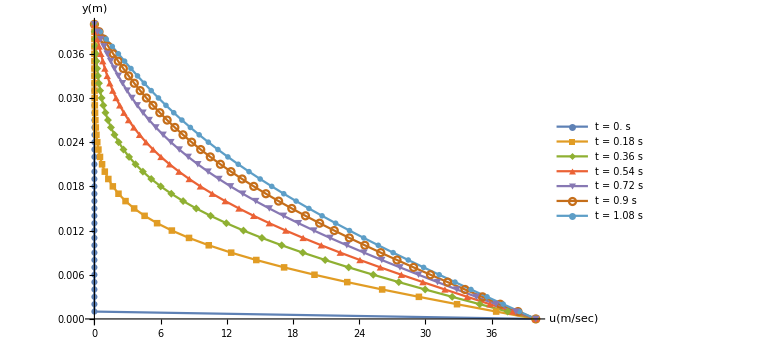

```mathematica
plots =MapThread[{#1,#2}&,{uReq[[#]],y}]&/@Range[1,Length[uReq]];
ListLinePlot[plots, PlotMarkers->Automatic,PlotLegends->tLabel ,AxesLabel->{"u(m/sec)","y(m)"},ImageSize->Large]
```